ΜΣΜ 61  
4η Γραπτή Εργασία
Λυμπερίδης Σταύρος   Α.Μ.: 91076

Ασκηση 1

α)

H χαρακτηριστική εξίσωση είναι μ^2 + μ + λ = 0
 με λύσεις : μ_(1,2)= (-1± √(1-4λ))/2

    1. όταν λ<1/4
         η λύση είναι Y(x)= c_1 e^(μ_1 x)+ c_2 e^(μ_2 x)
        εφραρμόζοντας τις συνοριακές συνθήκες βρίσκουμε ότι η μοναδική λύση είναι η τετριμμένη

    2. όταν λ=1/4
         η λύση είναι Y(x)= c_1 e^(-x/2)+ c_2 x e^(-x/2)
         εφραρμόζοντας τις συνοριακές συνθήκες βρίσκουμε ότι η μοναδική λύση είναι η τετριμμένη

    3. όταν λ>1/4
	έχουμε  Y(x)= e^(-x/2)( c_1 cos((√(4λ-1))/2 x)+ c_2 sin((√(4λ-1))/2 x))
	εφαρμόζοντας την συνθήκη Y(0)=0 βρίσκουμε  c_1=0
          εφαρμόζοντας την συνθήκη Y(π)=0 βρίσκουμε  
          e^(-π/2)c_2 sin((√(4λ-1))/2 π)=0
          για να μην οδηγηθούμε στην τετριμμένη λύση πρέπει:
   sin((√(4λ-1))/2 π)=0   άρα (√(4 λ_n-1))/2 π = n π  
          δηλαδή λ_n=1/4+n^2
          οπότε έχουμε τις ιδιοσυναρτήσεις:
   Y_n(x)=e^(-x/2)sin(nx)

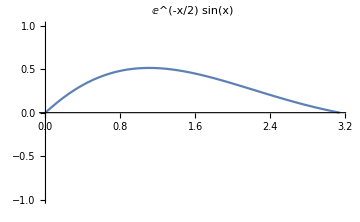
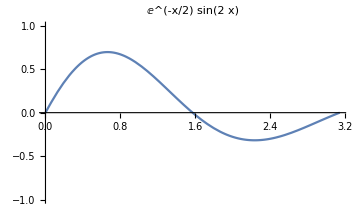
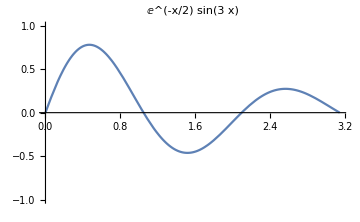
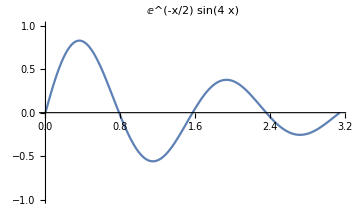

```mathematica
Clear["Global`*"]
Y[x_,n_]:=E^(-x/2) *Sin[n*x]
Table[Plot[Y[x,n],{x,0,Pi},PlotRange->{-1,1},ImageSize->Medium,PlotLabel->Y[x,n]],{n,1,4}]
```

β)

```mathematica
Clear["Global`*"]
NormYn=FullSimplify[Sqrt[Integrate[(Exp[-x/2]*Sin[n*x])^2,{x,0,Pi}]],n∈Integers&& n≥1];
Print["‖Y_n‖ = ",NormYn]
```

‖Y_n‖ = (ⅇ^(-π/2) √(2 (-1+ⅇ^π)) n)/(√(1+4 n^2))

γ)

```mathematica
Clear["Global`*"]
Y[x_,n_]=Exp[-x/2] *Sin[n*x];
NormY[x_,n_]=Simplify[Sqrt[Integrate[(Exp[-x/2] *Sin[n*x])^2,{x,0,Pi}]],n∈Integers && n≥1];
Print["‖Y_n‖ = ",NormY[x,n]]

X[x_,n_]=Simplify[Y[x,n]/NormY[x,n],n∈Integers && n≥1];
Print["X_n(x) = ",X[x,n]]

Result=FullSimplify[Integrate[X[x,n]*X[x,m],{x,0,Pi}],n∈Integers && m∈Integers && n≥1 && m≥1&& m!=n];
Print["\n< X_n , X_m > = ",Result," ≠ 0"]
Print["Άρα οι ιδιοσυναρτήσεις που αντιστοιχούν σε διακεκριμένες ιδιοτιμές δεν είναι κάθετες ως προς το εσωτερικό γινόμενο."]
```

‖Y_n‖ = (ⅇ^(-π/2) √(2 (-1+ⅇ^π)) n)/(√(1+4 n^2))

X_n(x) = (ⅇ^((π-x)/2) √(1+4 n^2) Sin[n x])/(√(2 (-1+ⅇ^π)) n)

< X_n , X_m > = (((-1)^(1+m+n)+ⅇ^π) √((1+4 m^2) (1+4 n^2)))/((-1+ⅇ^π) (1+(m-n)^2) (1+(m+n)^2)) ≠ 0

Άρα οι ιδιοσυναρτήσεις που αντιστοιχούν σε διακεκριμένες ιδιοτιμές δεν είναι κάθετες ως προς το εσωτερικό γινόμενο.

δ)

Οι γραφικές παραστάσεις των αθροισμάτων S_n για διάφορες τιμές του n :

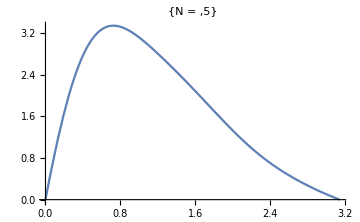
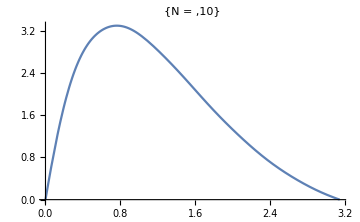
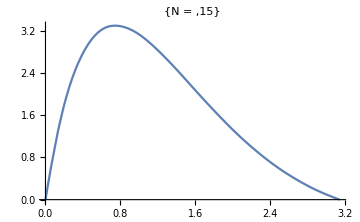
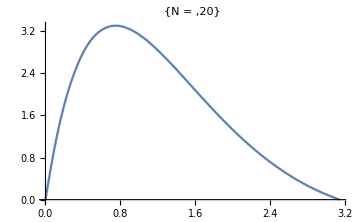

Οι γραφική παράσταση της f(x) :

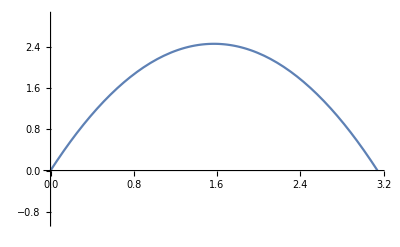

Παρατηρούμε ότι η σειρά δεν συγκλίνει.

```mathematica
Clear["Global`*"]

f[x_]:=x*(Pi-x)
Y[x_,n_]=(E^(-x/2)) *Sin[n*x];
NormY[x_,n_]=Simplify[Sqrt[Integrate[((E^(-x/2))*Sin[n*x])^2,{x,0,Pi}]],n∈Integers && n≥1];
X[x_,n_]=FullSimplify[(Y[x,n])/ (NormY[x,n]),n∈Integers && n≥1];

CN[n_]=FullSimplify[Integrate[f[x]*X[x,n],{x,0,Pi}],n∈Integers && n≥1];


SeriesF[x_,n_]:=Sum[ CN[i] * X[x,i],{i,n}]

Print["Οι γραφικές παραστάσεις των αθροισμάτων S_n για διάφορες τιμές του n :"]
Table[Plot[SeriesF[x,n],{x,0,Pi},PlotRange->All,ImageSize->Medium,PlotLabel->{"N = ",n}],{n,5,20,5}]

Print["Οι γραφική παράσταση της f(x) :"]
Plot[f[x],{x,0,Pi},PlotRange->{-1,3}]

Print["Παρατηρούμε ότι η σειρά δεν συγκλίνει."]
```

Ασκηση 2

α)

```mathematica
Clear["Global`*"]
(* Καταλλήγουμε ότι για λ>0 η λύση είναι η παρακάτω: *)
X[x_]:=c1 * Cos[ Sqrt[λ] *x ] +c2 * Sin[ Sqrt[λ]*x]
(* Από την συνθήκη X(0)=0 βρίσκουμε ότι c1=0 *)
c1:=0
Print["Η παράγωγος της X(x):"]
DX[x_]=D[X[x],x]
Print["Εφαρμόζοντας την 2η συνθήκη βρίσκουμε:"]
Simplify[X[1]+DX[1]==0]
(*για να αποφύγουμε την τετρημένη λύση δηλαδή c2=0 
 πρέπει:  √λ Cos[√λ]+Sin[√λ]=0
αλλιώς:   √λ=-tan √λ
*)
```

Η παράγωγος της X(x):

c2 √λ Cos[x √λ]

Εφαρμόζοντας την 2η συνθήκη βρίσκουμε:

c2 (√λ Cos[√λ]+Sin[√λ])==0

β)

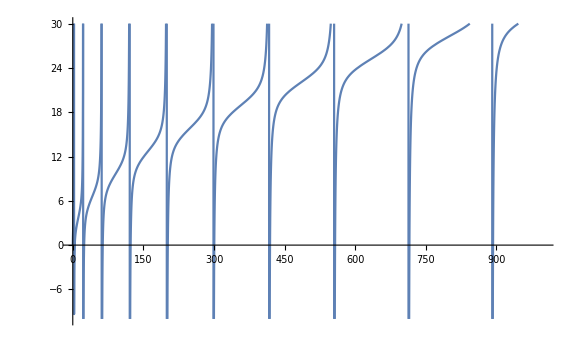

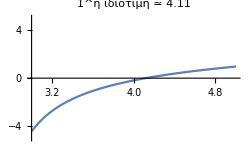
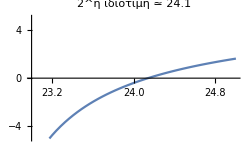
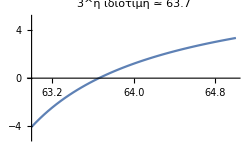
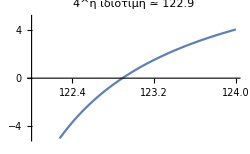
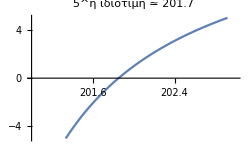
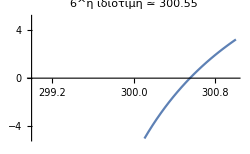
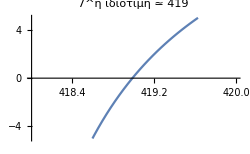

```mathematica
Clear["Global`*"]
F[x_]:= Sqrt[x]+Tan[Sqrt[x]]
Plot[F[x],{x,0,1000},ImageSize->Large,PlotRange->{-10,30}]

graph[1]=Plot[F[x],{x,3,5},ImageSize->{250,250},PlotRange->{-5,5},PlotLabel->"1^η ιδιοτιμή ≃ 4.11"];
b[1]=4.11;
graph[2]=Plot[F[x],{x,23,25},ImageSize->{250,250},PlotRange->{-5,5},PlotLabel->"2^η ιδιοτιμή ≃ 24.1"];
b[2]=24.1;
graph[3]=Plot[F[x],{x,63,65},ImageSize->{250,250},PlotRange->{-5,5},PlotLabel->"3^η ιδιοτιμή ≃ 63.7"];
b[3]=63.7;
graph[4]=Plot[F[x],{x,122,124},ImageSize->{250,250},PlotRange->{-5,5},PlotLabel->"4^η ιδιοτιμή ≃ 122.9"];
b[4]=122.9;
graph[5]=Plot[F[x],{x,201,203},ImageSize->{250,250},PlotRange->{-5,5},PlotLabel->"5^η ιδιοτιμή ≃ 201.7"];
b[5]=201.7;
graph[6]=Plot[F[x],{x,299,301},ImageSize->{250,250},PlotRange->{-5,5},PlotLabel->"6^η ιδιοτιμή ≃ 300.55"];
b[6]=300.55;
graph[7]=Plot[F[x],{x,418,420},ImageSize->{250,250},PlotRange->{-5,5},PlotLabel->"7^η ιδιοτιμή ≃ 419"];
b[7]=419;
graph[8]=Plot[F[x],{x,556,558},ImageSize->{250,250},PlotRange->{-5,5},PlotLabel->"8^η ιδιοτιμή ≃ 557.15"];
b[8]=557.15;
graph[9]=Plot[F[x],{x,714,716},ImageSize->{250,250},PlotRange->{-5,5},PlotLabel->"9^η ιδιοτιμή ≃ 715.05"];
b[9]=715.05;
graph[10]=Plot[F[x],{x,891,893},ImageSize->{250,250},PlotRange->{-5,5},PlotLabel->"10^η ιδιοτιμή ≃ 892.6"];
b[10]=892.6;

Table[graph[n],{n,1,10}]
```

γ)

```mathematica
F[x_]:= Sqrt[x]+Tan[Sqrt[x]]

(*Χρησιμοποιούμε τα αποτελέσματα από το β)*)
c[1]=x/.FindRoot[F[x],{x,4.11}]
c[2]=x/.FindRoot[F[x],{x,24.1}]
c[3]=x/.FindRoot[F[x],{x,63.7}]
c[4]=x/.FindRoot[F[x],{x,122.9}]
c[5]=x/.FindRoot[F[x],{x,201.7}]
c[6]=x/.FindRoot[F[x],{x,300.55}]
c[7]=x/.FindRoot[F[x],{x,419}]
c[8]=x/.FindRoot[F[x],{x,557.15}]
c[9]=x/.FindRoot[F[x],{x,715.05}]
c[10]=x/.FindRoot[F[x],{x,892.6}]
```

4.11586

24.1393

63.6591

122.889

201.851

300.55

418.987

557.162

715.077

892.73

δ)

```mathematica
L[n_]:=((2n-1)^2 Pi^2)/4

data=Table[{n,b[n],c[n],N[L[n]]},{n,1,10}];
TableForm[data,TableAlignments->Center,TableHeadings ->{None,{"ιδιοτιμή" ,"λύση β)","λύση γ)","ασυμπτωτική εκτίμηση"}}] 
Print["Παρατηρούμε ότι οι τιμές του λ_n είναι τα σημεία που δεν ορίζεται η συνάρτηση F(x)=√λ+tan(√λ)"]
Print["Επίσης παρατηρούμε ότι αν αυξήσουμε κατά 2 τις τιμές του λ_n πέρνουμε μια καλή προσέγγιση των ριζών της παραπάνω συνάρτησης όσο αυξάνεται το n"]
```

ιδιοτιμή | λύση β) | λύση γ) | ασυμπτωτική εκτίμηση
1 | 4.11 | 4.11586 | 2.4674
2 | 24.1 | 24.1393 | 22.2066
3 | 63.7 | 63.6591 | 61.685
4 | 122.9 | 122.889 | 120.903
5 | 201.7 | 201.851 | 199.859
6 | 300.55 | 300.55 | 298.556
7 | 419 | 418.987 | 416.991
8 | 557.15 | 557.162 | 555.165
9 | 715.05 | 715.077 | 713.079
10 | 892.6 | 892.73 | 890.732

Παρατηρούμε ότι οι τιμές του λ_n είναι τα σημεία που δεν ορίζεται η συνάρτηση F(x)=√λ+tan(√λ)

Επίσης παρατηρούμε ότι αν αυξήσουμε κατά 2 τις τιμές του λ_n πέρνουμε μια καλή προσέγγιση των ριζών της παραπάνω συνάρτησης όσο αυξάνεται το n

Ασκηση 3

α)

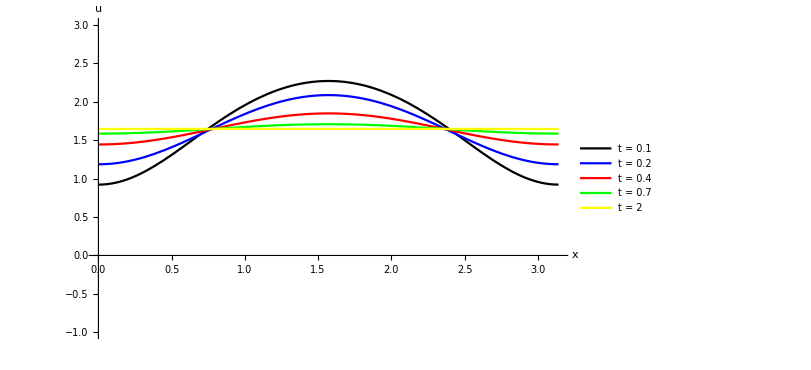

```mathematica
Clear["Global`*"]
c[n_,L_]:=2/L*∫_0^L f[x]*Cos[n*π*x/L]ⅆx
c0[L_]:=1/L*∫_0^L f[x]ⅆx
λ[n_,L_]:=(n^2*π^2)/L^2
U[x_,t_,N_,L_]:=c0[L]+∑_(n=1)^N c[n,L]*Exp[-λ[n,L]*t]*Cos[n*π*x/L]
f[x_]=x(Pi-x);

u[x_]=U[x,0.1,10,Pi];
plot1=Plot[u[x],{x,0,Pi},PlotRange->{-1,3},AxesLabel->{x,u},PlotLegends->{"t = 0.1"},PlotStyle->{Black},ImageSize->{600,400}];
u[x_]=U[x,0.2,10,Pi];
plot2=Plot[u[x],{x,0,Pi},PlotRange->{-1,3},AxesLabel->{x,u},PlotLegends->{"t = 0.2"},PlotStyle->{Blue},ImageSize->{600,400}];
u[x_]=U[x,0.4,10,Pi];
plot3=Plot[u[x],{x,0,Pi},PlotRange->{-1,3},AxesLabel->{x,u},PlotLegends->{"t = 0.4"},PlotStyle->{Red},ImageSize->{600,400}];
u[x_]=U[x,0.7,10,Pi];
plot4=Plot[u[x],{x,0,Pi},PlotRange->{-1,3},AxesLabel->{x,u},PlotLegends->{"t = 0.7"},PlotStyle->{Green},ImageSize->{600,400}];
u[x_]=U[x,2,10,Pi];
plot5=Plot[u[x],{x,0,Pi},PlotRange->{-1,3},AxesLabel->{x,u},PlotLegends->{"t = 2"},PlotStyle->{Yellow},ImageSize->{600,400}];

Show[plot1,plot2,plot3,plot4,plot5]
```

β)

Το πρόβλημα μετασχηματίζεται στο εξής:
v_t(x,t)=2 v_xx(x,t)                             , 0<x<π   ,t>0
v_x(0,t)=v_x(π,t)=0                           , t≥0
v(x,0)=1-cos(2x)+4cos(3x)    ,0≤ x≤ π

Το οποίο έχει λύση :
v(x,t)=c_0+∑_(n=1)^∞ c_n e^-λ_nt cos (n x)
c_0=1/Pi∫_0^Pi f(x) ⅆx    
c_n=2/Pi∫_0^Pi f(x)cos (n x) ⅆx      ,n≥1

εφαρμόζοντας τη δεύτερη συνθήκη θέτοντας για t=0 στην λύση πέρνουμε:
v(x,0)=c_0+∑_(n=1)^∞ c_n cos (n x)=1-cos(2x)+4cos(3x)
άρα βρίσκουμε ότι 
c_0=1 
c_1=0
c_2=-1
c_3=4  
c_n=0  όταν n≥4 

οπότε η λύση του μετασχηματισμένου προβλήματος είναι:
v(x,t)=1-e^(-2t)cos (2 x)+4 e^(-3t)cos (3 x)   

αντιστρέφοντας τον μετασχηματισμό βρίσκουμε:
u(x,t)=e^t-e^-t cos (2 x)+4 e^(-2t)cos (3 x)

```mathematica
Clear["Global`*"]

f[x_]=1-Cos[2x]+4Cos[3x] ;

c0=1/Pi*∫_0^Pi f[x]ⅆx;
Print["c_0 = ",c0]
Print["Υπολογίζοντας το ολοκλήρωμα βρίσκουμε ότι ο συντελεστής c_0 είναι 1 ,όπως τον βρήκαμε παραπάνω"]
c[n_]=2/Pi*∫_0^Pi f[x]*Cos[n*x]ⅆx;
Print["Βρίσκουμε ότι  c_n = ",c[n]]
Print["Παρατηρούμε ότι τα c_n μηδενίζονται για κάθε τιμή του n εκτώς από τις: 2,3 όπου έχουμε απροσδιοριστία "]
Print["Υπολογίζουμε τα όρια:"]
Print["καθώς το n->2  , c_2 = ",Limit[c[n],n->2]]
Print["καθώς το n->3  , c_3 = ",Limit[c[n],n->3]]
```

c_0 = 1

Υπολογίζοντας το ολοκλήρωμα βρίσκουμε ότι ο συντελεστής c_0 είναι 1 ,όπως τον βρήκαμε παραπάνω

Βρίσκουμε ότι  c_n = -(8 (-9-3 n^2+n^4) Sin[n π])/(n (-9+n^2) (-4+n^2) π)

Παρατηρούμε ότι τα c_n μηδενίζονται για κάθε τιμή του n εκτώς από τις: 2,3 όπου έχουμε απροσδιοριστία

Υπολογίζουμε τα όρια:

καθώς το n->2  , c_2 = -1

καθώς το n->3  , c_3 = 4

γ)

```mathematica
Clear["Global`*"]
Heat2=V/.First[NDSolve[{D[V[x,t], t]==2*D[V[x,t], {x,2}]+V[x,t],V[x,0]==1-Cos[2x]+4Cos[3x],(D[V[x,t],x]/.x->0)==0,(D[V[x,t],x]/.x->Pi)==0},{V},{t,0,10},{x,0,Pi},MaxStepSize->10000,MaxSteps->10000]];

Print["To γράφημα της λύσης που προκύπτει από την NDSolve: "]
fig1=Plot3D[Heat2[x,t],{t,0,7},{x,0,Pi},PlotRange->All,ColorFunction->"RustTones"]

u[x_,t_]=E^t-E^-t Cos[2 x]+4 E^(-2t)Cos[3 x];
Print["To γράφημα της λύσης που προκύπτει από το ερώτημα β): "]
fig2=Plot3D[u[x,t], {t,0,7},{x,0,Pi},PlotRange->All,ColorFunction->"BlueGreenYellow"]

Print["Tα γράφηματα των δύο λύσεων μαζί: "]
Show[fig1,fig2]
Print["Παρατηρούμε ότι η μέθοδος NDSolve δίνει αποτελέσματα με μεγάλη ακρίβεια."]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

To γράφημα της λύσης που προκύπτει από την NDSolve:

-Graphics3D-

To γράφημα της λύσης που προκύπτει από το ερώτημα β):

-Graphics3D-

Tα γράφηματα των δύο λύσεων μαζί:

-Graphics3D-

Παρατηρούμε ότι η μέθοδος NDSolve δίνει αποτελέσματα με μεγάλη ακρίβεια.

Ασκηση 4

α)

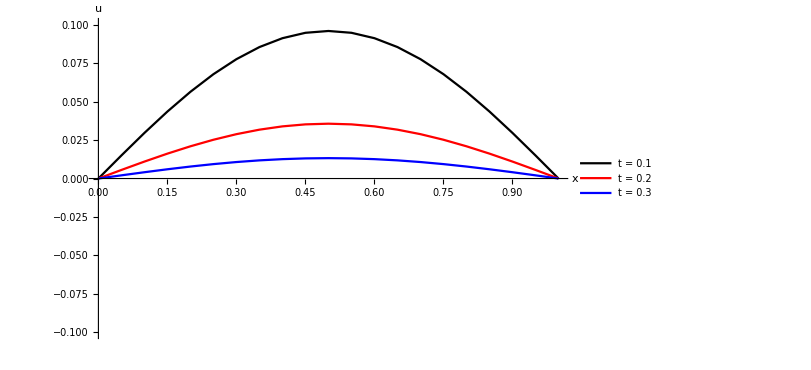

-Graphics3D-

```mathematica
Clear["Global`*"]
SetOptions[ListPlot,Joined->True];f[x_]:=x*(1-x);nu=1;nX=20;nT=1000;l=1;tF=1;h=l/nX;k=tF/nT;r=N[nu*k/h^2];
Table[xN[i]=i*h,{i,0,nX}];
Table[tN[j]=j*k,{j,0,nT}];
ic=Table[uN[i,0]->f[xN[i]],{i,0,nX}];
bc={Table[uN[0,j]->0,{j,0,nT}],Table[uN[nX,j]->0,{j,0,nT}]};
ibc=Flatten[{ic,bc}];
fd[i_,j_]:=(1-2*r)*uN[i,j]+r*(uN[i+1,j]+uN[i-1,j]);
Do[uN[i,j+1]=fd[i,j]/.ibc,{j,0,nT},{i,1,nX-1}];

plot1=ListPlot[Table[{xN[i],uN[i,100]/.ibc},{i,0,nX}],AxesLabel->{"x","u"},PlotRange->{-0.1,0.1},PlotLegends->{"t = 0.1"},PlotStyle->{Black},ImageSize->{600,400}];
plot2=ListPlot[Table[{xN[i],uN[i,200]/.ibc},{i,0,nX}],AxesLabel->{"x","u"},PlotRange->{-0.1,0.1},PlotLegends->{"t = 0.2"},PlotStyle->{Red}];
plot3=ListPlot[Table[{xN[i],uN[i,300]/.ibc},{i,0,nX}],AxesLabel->{"x","u"},PlotRange->{-0.1,0.1},PlotLegends->{"t = 0.3"},PlotStyle->{Blue}];
Show[plot1,plot2,plot3]

data=Flatten[Table[{xN[i],tN[j],uN[i,j]/.ibc},{j,0,nT},{i,0,nX}],1];
fig1=ListPlot3D[data,AxesLabel->{Style[x,Blue,Bold,12],Style[t,Blue,Bold,12],Style[u,Blue,Bold,12]},LabelStyle->Directive[Brown,Opacity[0.7]],ColorFunction->"TemperatureMap",Mesh->4,
ImageSize->{600,400},PlotRange->{-0.3,0.3}]
```

β)

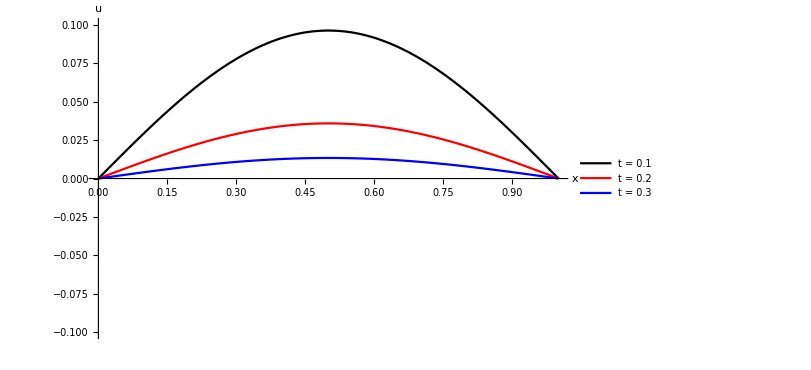

-Graphics3D-

```mathematica
f[x_]=x*(1-x);
c[n_,L_]:=2/L*∫_0^L f[x]*Sin[n*π*x/L]ⅆx
λ[n_,L_]:=(n^2*π^2)/L^2
U[x_,t_,N_,L_]:=∑_(n=1)^N c[n,L]*Exp[-λ[n,L]*t]*Sin[n*π*x/L]

ub[x_,t_]=U[x,t,10,1];


plotb1=Plot[ub[x,0.1],{x,0,1},AxesLabel->{"x","u"},PlotRange->{-0.1,0.1},PlotLegends->{"t = 0.1"},PlotStyle->{Black},ImageSize->{600,400}];
plotb2=Plot[ub[x,0.2],{x,0,1},AxesLabel->{"x","u"},PlotRange->{-0.1,0.1},PlotLegends->{"t = 0.2"},PlotStyle->{Red}];
plotb3=Plot[ub[x,0.3],{x,0,1},AxesLabel->{"x","u"},PlotRange->{-0.1,0.1},PlotLegends->{"t = 0.3"},PlotStyle->{Blue}];

Show[plotb1,plotb2,plotb3]

fig2=Plot3D[ub[x,t], {t,0,1},{x,0,1},PlotRange->{-0.3,0.3},Mesh->4,ColorFunction->"TemperatureMap",ImageSize->{600,400}]
```

γ)

```mathematica
solution=V/.First[NDSolve[{D[V[x,t], t]==D[V[x,t], {x,2}],V[x,0]==x*(1-x),V[0,t]==0,V[1,t]==0},{V},{t,0,10},{x,0,1},MaxStepSize->10000,MaxSteps->10000]];

plotc1=Plot[solution[x,0.1],{x,0,1},AxesLabel->{"x","u"},PlotRange->{-0.1,0.1},PlotLegends->{"t = 0.1"},PlotStyle->{Black},ImageSize->{600,400}];
plotc2=Plot[solution[x,0.2],{x,0,1},AxesLabel->{"x","u"},PlotRange->{-0.1,0.1},PlotLegends->{"t = 0.2"},PlotStyle->{Red}];
plotc3=Plot[solution[x,0.3],{x,0,1},AxesLabel->{"x","u"},PlotRange->{-0.1,0.1},PlotLegends->{"t = 0.3"},PlotStyle->{Blue}];

Show[plotb1,plotb2,plotb3]

fig3=Plot3D[solution[x,t],{t,0,1},{x,0,1},PlotRange->{-0.3,0.3},Mesh->4,ColorFunction->"TemperatureMap",ImageSize->{600,400}]
```

-Graphics-

-Graphics3D-

δ)

```mathematica
data2=Table[{i*0.05,uN[i,100],ub[0.05*i,0.1],solution[0.05*i,0.1]},{i,1,19}] ;
data3=Table[{i*0.05,uN[i,300],ub[0.05*i,0.3],solution[0.05*i,0.3]},{i,1,19}] ;
Print["Αποτελέσματα για την χρονική στιγμή t = 0.1 :"]
TableForm[data2, TableAlignments->Center,TableHeadings->{{},{"κόμβος χ","Λύση α)","Λύση β)","Λύση γ)"}}]
Print["Αποτελέσματα για την χρονική στιγμή t = 0.3 :"]
TableForm[data3, TableAlignments->Center,TableHeadings->{{},{"κόμβος χ","Λύση α)","Λύση β)","Λύση γ)"}}]
```

Αποτελέσματα για την χρονική στιγμή t = 0.1 :

| κόμβος χ | Λύση α) | Λύση β) | Λύση γ)
 | 0.05 | 0.0150008 | 0.0150438 | 0.0150557
 | 0.1 | 0.0296321 | 0.0297171 | 0.0297386
 | 0.15 | 0.0435336 | 0.0436585 | 0.0436856
 | 0.2 | 0.056363 | 0.0565246 | 0.0565524
 | 0.25 | 0.0678044 | 0.0679986 | 0.0680225
 | 0.3 | 0.077576 | 0.0777981 | 0.0778145
 | 0.35 | 0.0854374 | 0.0856818 | 0.0856893
 | 0.4 | 0.0911951 | 0.0914559 | 0.091455
 | 0.45 | 0.0947073 | 0.0949781 | 0.0949713
 | 0.5 | 0.0958878 | 0.0961619 | 0.0961529
 | 0.55 | 0.0947073 | 0.0949781 | 0.0949713
 | 0.6 | 0.0911951 | 0.0914559 | 0.091455
 | 0.65 | 0.0854374 | 0.0856818 | 0.0856893
 | 0.7 | 0.077576 | 0.0777981 | 0.0778145
 | 0.75 | 0.0678044 | 0.0679986 | 0.0680225
 | 0.8 | 0.056363 | 0.0565246 | 0.0565524
 | 0.85 | 0.0435336 | 0.0436585 | 0.0436856
 | 0.9 | 0.0296321 | 0.0297171 | 0.0297386
 | 0.95 | 0.0150008 | 0.0150438 | 0.0150557

Αποτελέσματα για την χρονική στιγμή t = 0.3 :

| κόμβος χ | Λύση α) | Λύση β) | Λύση γ)
 | 0.05 | 0.00207185 | 0.00208967 | 0.00208554
 | 0.1 | 0.00409268 | 0.00412789 | 0.00411972
 | 0.15 | 0.00601273 | 0.00606447 | 0.00605247
 | 0.2 | 0.00778474 | 0.00785172 | 0.00783619
 | 0.25 | 0.00936505 | 0.00944563 | 0.00942695
 | 0.3 | 0.0107148 | 0.010807 | 0.0107856
 | 0.35 | 0.0118007 | 0.0119022 | 0.0118787
 | 0.4 | 0.012596 | 0.0127043 | 0.0126793
 | 0.45 | 0.0130811 | 0.0131937 | 0.0131676
 | 0.5 | 0.0132442 | 0.0133581 | 0.0133318
 | 0.55 | 0.0130811 | 0.0131937 | 0.0131676
 | 0.6 | 0.012596 | 0.0127043 | 0.0126793
 | 0.65 | 0.0118007 | 0.0119022 | 0.0118787
 | 0.7 | 0.0107148 | 0.010807 | 0.0107856
 | 0.75 | 0.00936505 | 0.00944563 | 0.00942695
 | 0.8 | 0.00778474 | 0.00785172 | 0.00783619
 | 0.85 | 0.00601273 | 0.00606447 | 0.00605247
 | 0.9 | 0.00409268 | 0.00412789 | 0.00411972
 | 0.95 | 0.00207185 | 0.00208967 | 0.00208554

Ασκηση 5

α)

Όπως στο βιβλίο σελ. 21-26.
Επειδή έχουμε ότι g(x)=0 θα μηδενιστούν οι συντελεστές b_n οπότε η λύση παίρνει την ζητούμενη μορφή.

β)

εφαρμόζοντας τη  συνθήκη θέτοντας για t=0 στην λύση πέρνουμε:
u(x,0)=∑_(n=1)^∞ c_n sin(n x) =f(x)=2Sin[x]-3Sin[2x]+4Sin[5x]

άρα βρίσκουμε ότι :
c_1=2
c_2=-3
c_3=0  
c_4=0 
c_5=4 
c_n=0  όταν n≥6 

οπότε η λύση του  προβλήματος είναι:
u(x,t)= 2 Cos[2 t] Sin[x]-3 Cos[4 t] Sin[2 x]+4 Cos[10 t] Sin[5 x]

```mathematica
Clear["Global`*"]
c:=2
L:=Pi
ω=Pi*c/L;
f[x_]=2Sin[x]-3Sin[2x]+4Sin[5x];
g[x_]=0;
U[x_,t_,MaxN_,L_]:=Sum[a[n,L]*Cos[n*ω*t]*Sin[n*π*x/L],{n,1,MaxN}]
a[n_,L_]:=2/L*Integrate[f[x]*Sin[n*π*x/L],{x,0,L}]

u[x_,t_]=U[x,t,10,Pi];
Print["H λύση είναι η u(x,t) = ",u[x,t]]
Print["Η σειρά της λύσης περιλαμβάνει 3 όρους "]
Print["To γράφημα της λύσης:"]
Plot3D[u[x,t], {t,0,10},{x,0,Pi},PlotRange->All,ColorFunction->"BlueGreenYellow"]
```

H λύση είναι η u(x,t) = 2 Cos[2 t] Sin[x]-3 Cos[4 t] Sin[2 x]+4 Cos[10 t] Sin[5 x]

Η σειρά της λύσης περιλαμβάνει 3 όρους

To γράφημα της λύσης:

-Graphics3D-

Ασκηση 6

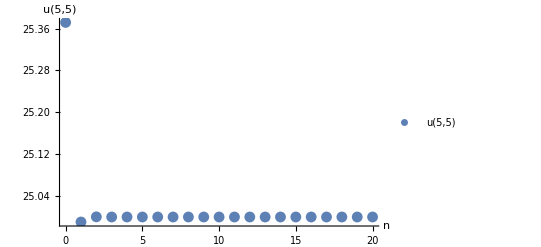

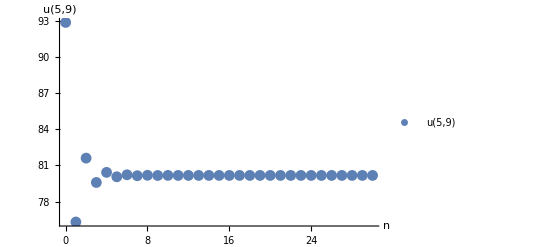

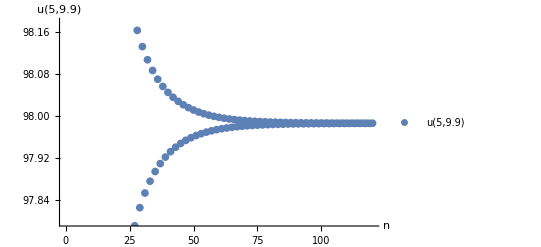

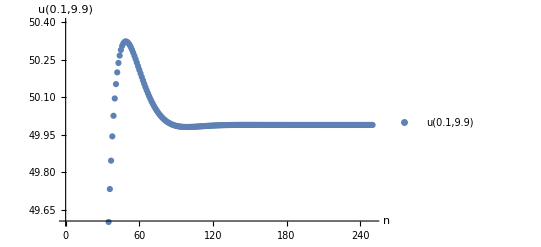

```mathematica
Clear["Global`*"]
Subscript[V, 0]:=100
L:=10

u[x_,y_,N_]=(4 Subscript[V, 0])/Pi Sum[1/((2n+1) Sinh[(2n+1) *Pi])Sin[((2n+1) *Pi*x)/L]Sinh[((2n+1) *Pi*y)/L],{n,0,N}];


ListPlot[Table[{n,u[5,5,n]},{n,0,20}],PlotRange->All,AxesLabel->{n,"u(5,5)"},PlotLegends->{"u(5,5)"}]
ListPlot[Table[{n,u[5,9,n]},{n,0,30}],PlotRange->All,AxesLabel->{n,"u(5,9)"},PlotLegends->{"u(5,9)"}]
ListPlot[Table[{n,u[5,9.9,n]},{n,0,120}],AxesLabel->{n,"u(5,9.9)"},PlotLegends->{"u(5,9.9)"}]
ListPlot[Table[{n,u[0.1,9.9,n]},{n,0,250}],PlotRange->{49.60,50.40},AxesLabel->{n,"u(0.1,9.9)"},PlotLegends->{"u(0.1,9.9)"}]
```

Παρατηρούμε ότι στις δύο πρώτες περιπτώσεις η σειρά συγκλίνει σχετικά γρήγορα.
Πράγμα αναμενόμενο καθώς στην πρώτη περίπτωση το σημείο βρίσκεται στο κέντρο του τετραγώνου ενώ στην δεύτερη περίπτωση βρίσκεται κοντά στον οπλισμό του πυκνωτή(την μεταλλική λορίδα) όχι όμως τόσο κοντά όσο την τρίτη περίπτωση όπου παρατηρούμε ότι χρειάζεται αρκετά μεγαλύτερος αριθμός του n ώστε να συγκλίνει η σειρά.
Τέλος στην τέταρτη περίπτωση το σημείο πλησιάζει το μονωτικό υλικό που βρίσκεται ανάμεσα στους δύο οπλισμούς του πυκνωτή οπότε αναμένουμε να υπάρχει πρόβλημα όσο πλησιάζουμε αυτό το σημείο καθώς το ηλεκτρικό πεδίο απειρίζεται πράγμα το οποίο επιβεβαιώνεται από το γράφημα καθώς παρατηρούμε μεγαλύτερη διακύμανση των τιμών για ακρετά μεγάλο αριθμό του n μέχρι να αρχίσει να συγκλίνει η σειρά.